# Statistics for Brody Fits

### Read in data from Fortran code to generate statistical distributions

```mathematica
initialspacings=Import["~/Code/Nchannel/Square/CODES/dos/fort.99","Table"];
```

```mathematica
initialspacings;
```

```mathematica
pos=Flatten[Evaluate[Differences[initialspacings[[1;;19]]]]]
```

Thread::tdlen: Objects of unequal length in {}-{1.51179} cannot be combined.

Thread::tdlen: Objects of unequal length in {-9.81675}-{} cannot be combined.

{0.447208,2.31293,0.490236,2.20044,2.59129,0.103448,1.898,1.41468,{}-{1.51179},{-9.81675}-{},0.403858,1.15926,0.943281,2.20663,2.06201,1.72503,1.36272,2.84654}

0.301632

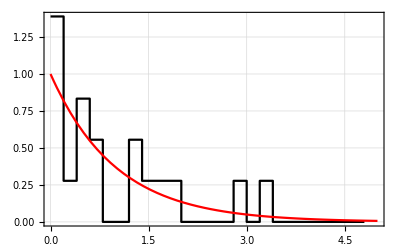

```mathematica
avgd=Mean[pos]
dx=0.2;
pos1=pos/avgd;
bins=Table[x,{x,0,5,dx}];
bc1=BinCounts[pos1,{bins}];
bcnorm=Table[{bins[[i]],bc1[[i]]/Total[bc1]/dx},{i,1,Length[bins]-1}];
Show[ListPlot[bcnorm,PlotRange->All,InterpolationOrder->0,Joined->True,PlotStyle->Black],Plot[Exp[-x],{x,0,5},PlotStyle->Red],PlotRange->All,Frame->True,GridLines->Automatic]
```

### Brody Parameter

Fit the level spacing distribution to:

```mathematica
PBrody[w_,x_]:=(1+w)(Gamma[(2+w)/(1+w)])^(1+w)x^w Exp[-(Gamma[(2+w)/(1+w)]x)^(1+w)];
αBrody[w_]:=Gamma[(2+w)/(1+w)]^(1+w);
ABrody[w_]:=αBrody[w](1+w);
```

```mathematica
CBrody[w_,z_]:=1-Exp[-αBrody[w] z^(1+w)]
```

```mathematica
D[CBrody[w,z],z]
```

ⅇ^(-z^(1+w) Gamma[(2+w)/(1+w)]^(1+w)) (1+w) z^w Gamma[(2+w)/(1+w)]^(1+w)

```mathematica
Solve[u==CBrody[w,z],z]//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{z→(-Gamma[(2+w)/(1+w)]^(-1-w) Log[1-u])^(1/(1+w))}}

```mathematica
BrodySample[w_,n_]:=Module[{u,z},u=RandomReal[{0,1},n];(-Gamma[(2+w)/(1+w)]^(-1-w) Log[1-u])^(1/(1+w))]
```

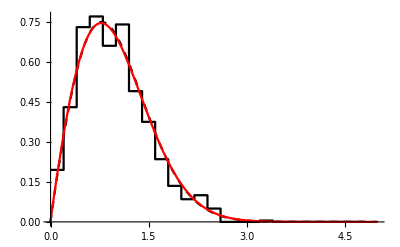

```mathematica
w0=0.954;
NP=1000;
dx=0.2;
Bins=Table[t,{t,0,5,dx}];
samp=BrodySample[w0,NP];
bc=BinCounts[samp,{Bins}]/NP/dx;
bnorm=Table[{(Bins[[i]]),bc[[i]]},{i,1,Length[Bins]-1}];
bfit=Table[{(Bins[[i]]+Bins[[i+1]])/2,bc[[i]]},{i,1,Length[Bins]-1}];
ph=ListPlot[bnorm,InterpolationOrder->0,Joined->True,PlotStyle->Black];
pe=Plot[PBrody[w0,z],{z,0,5},PlotStyle->{Black,Dashed}];
nlm=NonlinearModelFit[bfit,{PBrody[w,z]},{{w,0.0}},z,Method->"LevenbergMarquardt",ConfidenceLevel->0.99];
pb=Plot[PBrody[w/.nlm["BestFitParameters"],z],{z,0,5},PlotStyle->{Red}];
Show[{ph,pe,pb},PlotRange->All]
```

```mathematica
BinData=Import["~/Code/Nchannel/Square/CODES/dos/fort.400","Table"];
{NumEnsemble,NumLam,NumBins}=BinData[[1]];
Bins=BinData[[2]];
binsize=Bins[[2]]-Bins[[1]];
```

```mathematica
NumEnsemble
```

200

```mathematica
NumLam
```

40

```mathematica
BinData[[1]]
```

{200,40,19}

```mathematica
BDC=DeleteCases[BinData[[3;;Length[BinData]]],{}];
(*BDC=Select[BinData[[3;;Length[BinData]]],UnsameQ[#,{}]&];*)
```

```mathematica
Length[BinData]
Length[BDC]
```

3102

3000

```mathematica
BDC[[2]]
```

{1,2,0.13793,2.482,4,10,8,5,2,1,2,2,0,2,3,0,0,0,0,1,0,0,0,0}

```mathematica
BCAll=Table[Table[Select[BDC,#[[2]]==ilam&][[iens,5;;5+NumBins]],{iens,1,NumEnsemble}],{ilam,1,NumLam}];
```

```mathematica
BCNorms=Table[Table[Sum[BCAll[[ilam,iens,ibin]],{ibin,1,NumBins+1}],{iens,1,NumEnsemble}],{ilam,1,NumLam}];
```

```mathematica
BFits=Table[Table[Table[{(Bins[[ibin]]+Bins[[ibin+1]])/2,BCAll[[ilam,iens,ibin]]/(BCNorms[[ilam,iens]]binsize)},{ibin,1,NumBins}],{ilam,1,NumLam}],{iens,1,NumEnsemble}];
```

```mathematica
BCData=Table[Table[Table[{Bins[[ibin]],BCAll[[ilam,iens,ibin]]/(BCNorms[[ilam,iens]]binsize)},{ibin,1,NumBins}],{ilam,1,NumLam}],{iens,1,NumEnsemble}];
```

```mathematica
gccVals=Table[BDC[[ilam,3]],{ilam,1,NumLam}];
```

```mathematica
avgD=Table[Table[BDC[[NumLam(iens-1)+ilam,4]],{iens,1,NumEnsemble}],{ilam,1,NumLam}];
```

```mathematica
EnsAvgD=Table[Mean[avgD[[ilam]]],{ilam,1,NumLam}];
```

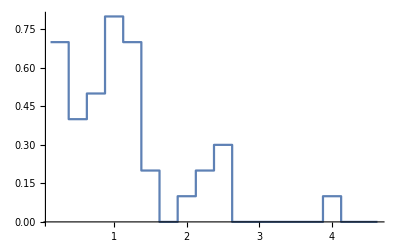

```mathematica
ListPlot[BFits[[1,10]],PlotRange->All,Joined->True,InterpolationOrder->0]
```

```mathematica
nlm=Table[Table[NonlinearModelFit[BFits[[iens,ilam]],{PBrody[w,z]},{{w,0.5}},z,ConfidenceLevel->0.9],{ilam,1,NumLam}],{iens,1,NumEnsemble}];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
wvals=Table[Table[w/.nlm[[iens,ilam]]["BestFitParameters"],{iens,1,NumEnsemble}],{ilam,1,NumLam}];
BrodyAvg=Table[{{gccVals[[ilam]]/EnsAvgD[[ilam]],Mean[wvals[[ilam]]]},ErrorBar[StandardDeviation[wvals[[ilam]]]/(√NumEnsemble)]},{ilam,1,NumLam}];
```

```mathematica
BrodyAvg[[2]]
```

{{0.0555548,-0.0097933},ErrorBar[0.0225917]}

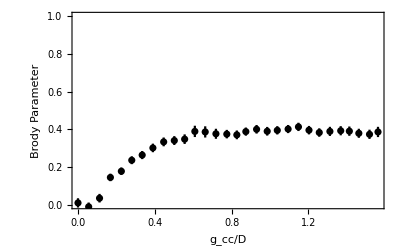

```mathematica
pavgs=ErrorListPlot[BrodyAvg,Frame->True,LabelStyle->Medium,PlotRange->{0,1.0},FrameLabel->{"g_cc/D","Brody Parameter"},PlotStyle->Black]
```

```mathematica
BCTotals=Table[Table[{Bins[[ibin]],Sum[BCAll[[ilam,iens,ibin]],{iens,1,NumEnsemble}]/(Sum[BCNorms[[ilam,iens]],{iens,1,NumEnsemble}]binsize)},{ibin,1,NumBins+1}],{ilam,1,NumLam}];
BCTotalFits=Table[Table[{(Bins[[ibin]]+Bins[[ibin+1]])/2,Sum[BCAll[[ilam,iens,ibin]],{iens,1,NumEnsemble}]/(Sum[BCNorms[[ilam,iens]],{iens,1,NumEnsemble}]binsize)},{ibin,1,NumBins+1}],{ilam,1,NumLam}];
```

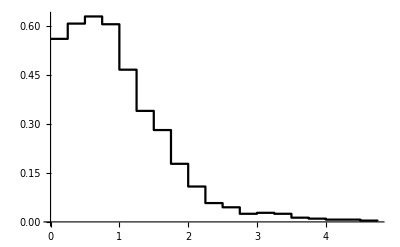

```mathematica
ListPlot[BCTotals[[20]],PlotStyle->Black,Joined->True,InterpolationOrder->0]
```

```mathematica
nlmT=Table[NonlinearModelFit[BCTotalFits[[ilam]],{PBrody[w,z]},{{w,0.5}},z,Method->"LevenbergMarquardt",ConfidenceLevel->0.9],{ilam,1,NumLam}];
```

```mathematica
wTotalvals=Table[w/.nlmT[[ilam]]["BestFitParameters"],{ilam,1,NumLam}];
```

```mathematica
nlmT[[2]]["ParameterErrors"]
```

{0.0189533}

```mathematica
BrodyTotAvg=Table[{{gccVals[[ilam]]/EnsAvgD[[ilam]],wTotalvals[[ilam]]},ErrorBar[nlmT[[ilam]]["ParameterErrors"][[1]]]},{ilam,1,NumLam}];
```

```mathematica
BrodyTotAvg[[1]]
```

{{0.,-0.00110421},ErrorBar[0.0185064]}

```mathematica
BrodyAvg[[1]]
```

{{0.,0.0108404},ErrorBar[0.0245508]}

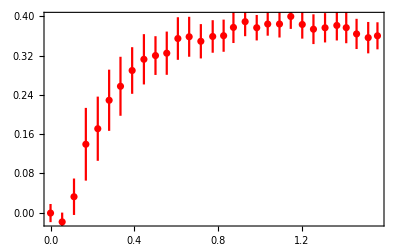

```mathematica
ptotfits=ErrorListPlot[BrodyTotAvg,Frame->True,LabelStyle->Medium,PlotStyle->Red]
```

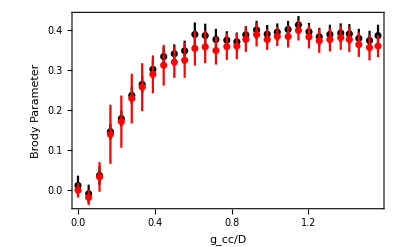

```mathematica
Show[pavgs,ptotfits,PlotRange->All]
```

### Bound state sector Brody Fits from fortran code

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
data=Import["~/Code/Nchannel/Square/CODES/dos/fort.700","Table"];
NumLam=Length[data];
avgw=Table[{{data[[ilam,2]],data[[ilam,3]]},ErrorBar[data[[ilam,4]]]},{ilam,1,NumLam}];
binallw=Table[{{data[[ilam,2]],data[[ilam,5]]},ErrorBar[data[[ilam,4]]]},{ilam,1,NumLam}];
```

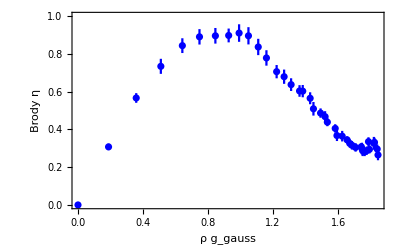

```mathematica
pbinallw=ErrorListPlot[binallw,Frame->True,LabelStyle->Large,PlotStyle->Blue,PlotRange->{0,1},FrameLabel->{"ρ g_gauss","Brody η"}];
Show[pbinallw]
```

```mathematica
Export["~/posters&talks/DAMOP-2018/figures/BoundSectorBrody-20Channel.pdf",pbinallw]
```

~/posters&talks/DAMOP-2018/figures/BoundSectorBrody-20Channel.pdf

Import the distributions to verify that these fits are good

```mathematica
BinData=Import["~/Code/Nchannel/Square/CODES/dos/fort.400","Table"];
{NumEnsemble,NumLam,NumBins}=BinData[[1]];
Bins=BinData[[2]];
binsize=Bins[[2]]-Bins[[1]];
```

```mathematica
distdata=Import["~/Code/Nchannel/Square/CODES/dos/fort.900","Table"];
```

```mathematica
distdata[[1]]
```

{1,0.,-0.0000153796,0.880223,0.686351,0.552646,0.393315,0.324234,0.248468,0.191643,0.141504,0.118106,0.118106,0.0924791,0.0791086,0.0412256,0.0445682,0.0278552,0.0256267,0.0155989,0.00557103,0.00668524,0.00668524}

```mathematica
bdist=Table[Table[{Bins[[ibin]],distdata[[ilam,ibin+3]]},{ibin,1,NumBins+1}],{ilam,1,NumLam}];
```

```mathematica
bdist[[1]]
```

{{0.,0.880223},{0.25,0.686351},{0.5,0.552646},{0.75,0.393315},{1.,0.324234},{1.25,0.248468},{1.5,0.191643},{1.75,0.141504},{2.,0.118106},{2.25,0.118106},{2.5,0.0924791},{2.75,0.0791086},{3.,0.0412256},{3.25,0.0445682},{3.5,0.0278552},{3.75,0.0256267},{4.,0.0155989},{4.25,0.00557103},{4.5,0.00668524},{4.75,0.00668524}}

```mathematica
ilamtest=30;ph=ListPlot[bdist[[ilamtest]],PlotStyle->Black,Joined->True,InterpolationOrder->0,PlotRange->All,Frame->True,LabelStyle->Large,FrameLabel->{"S/D","probability P(S)"}];
pbrody=Plot[PBrody[distdata[[ilamtest,3]],z],{z,0.0,5},PlotStyle->{Red}];distdata[[ilamtest,2]]
distdata[[ilamtest,3]]
```

1.74223

0.30827

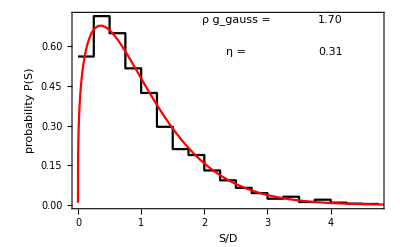

```mathematica
ptest1=Show[ph,pbrody,Epilog->{
Text[Style["ρ g_gauss = "],{2.5,0.7},FormatType->Large],
Text[Style[NumberForm[distdata[[ilamtest,2]],{2,2}]],{4,0.7},FormatType->Large],
Text[Style["η = "],{2.5,0.58},FormatType->Large],
Text[Style[NumberForm[distdata[[ilamtest,3]],{2,2}]],{4,0.58},FormatType->Large]}]
```

```mathematica
Export["~/posters&talks/DAMOP-2018/figures/ptest30.pdf",ptest1]
```

~/posters&talks/DAMOP-2018/figures/ptest30.pdf

```mathematica
pbrody=Plot[PBrody[w/.nlm[[ienstest,ilamtest]]["BestFitParameters"],z],{z,0.0,5},PlotStyle->{Red}];
```

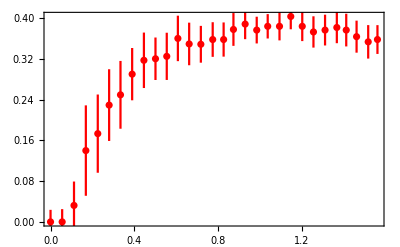

```mathematica
fortdata=Import["~/Code/Nchannel/Square/CODES/dos/DataFromMorgoth/20channel/fort.700","Table"];NumLam=Length[fortdata];
fortbrodyplotdata=Table[{{fortdata[[ilam,2]],fortdata[[ilam,3]]},ErrorBar[fortdata[[ilam,4]]]},{ilam,1,NumLam}];
fortbrodytotplotdata=Table[{{fortdata[[ilam,2]],fortdata[[ilam,5]]},ErrorBar[fortdata[[ilam,6]]]},{ilam,1,NumLam}];
(*fortfitplot10=ErrorListPlot[fortbrodyplotdata,Frame->True,LabelStyle->Medium,PlotStyle->Green];*)
fortfitplot20tot=ErrorListPlot[fortbrodytotplotdata,Frame->True,LabelStyle->Medium,PlotStyle->Red,PlotRange->All]
```

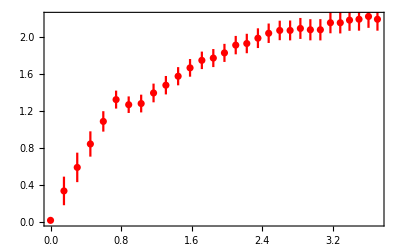

```mathematica
fortdata=Import["~/Code/Nchannel/Square/CODES/dos/DataFromMorgoth/40channel/fort.700","Table"];NumLam=Length[fortdata];
fortbrodyplotdata=Table[{{fortdata[[ilam,2]],fortdata[[ilam,3]]},ErrorBar[fortdata[[ilam,4]]]},{ilam,1,NumLam}];
fortbrodytotplotdata=Table[{{fortdata[[ilam,2]],fortdata[[ilam,5]]},ErrorBar[fortdata[[ilam,6]]]},{ilam,1,NumLam}];
(*fortfitplot10=ErrorListPlot[fortbrodyplotdata,Frame->True,LabelStyle->Medium,PlotStyle->Green];*)
fortfitplot40tot=ErrorListPlot[fortbrodytotplotdata,Frame->True,LabelStyle->Medium,PlotStyle->Red,PlotRange->All]
```

Okay, this graph shows the Brody parameter for three different runs: 10 channels, 40 channels, and 80 channels.  There is some evidence for a universal curve.  D = average energy level spacing.

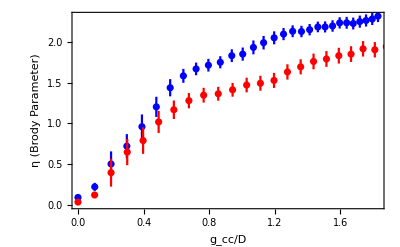

```mathematica
Show[fortfitplot10tot,fortfitplot20tot,FrameLabel->{"g_cc/D","η (Brody Parameter)"}]
```

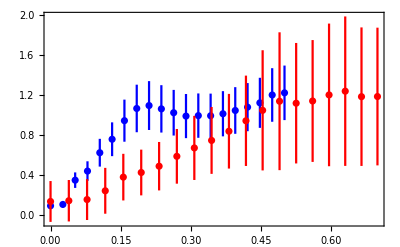

```mathematica
Show[fortfitplot40,fortfitplot20,PlotRange->All]
```

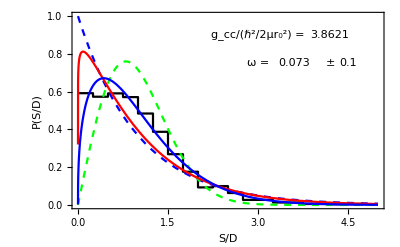

```mathematica
ilamtest=29;ienstest=1;
pp=Plot[{PBrody[0,x],PBrody[1,x]},{x,0,5},PlotStyle->{{Blue,Dashed},{Green,Dashed}}];
ph=ListPlot[BCTotals[[ilamtest]],PlotStyle->Black,Joined->True,InterpolationOrder->0,PlotRange->All];
pbrody=Plot[PBrody[w/.nlm[[ienstest,ilamtest]]["BestFitParameters"],z],{z,0.0,5},PlotStyle->{Red}];
pbrodyfort=Plot[PBrody[fortdata[[ilamtest,3]],z],{z,0.0,5},PlotStyle->{Blue}];
Show[{ph,pp,pbrody,pbrodyfort},Frame->True,PlotRange->All,Epilog->{
Text["g_cc/(ℏ^2/2μr_0^2) = ",{3,.9}],
Text[gccVals[[ilamtest]],{4.2,0.9}],
Text["ω = ",{3,.75}],
Text[NumberForm[w/.nlm[[ienstest,ilamtest]]["BestFitParameters"],2],{3.6,0.75}],
Text["±",{4.2,0.75}],
Text[NumberForm[nlm[[ienstest,ilamtest]]["ParameterErrors"][[1]],1],{4.5,0.75}]
(*Text["Avg Spacing D/(ℏ^2/2μr_0^2) = ",{3.0,0.6}],
Text[avgD[[ienstest,ilamtest]],{4.5,0.6}]*)
},LabelStyle->Large,FrameLabel->{"S/D","P(S/D)"}]
```

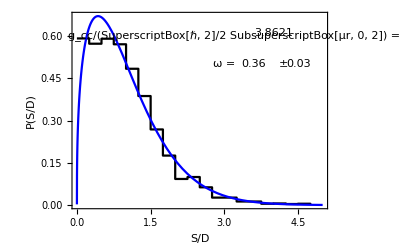

```mathematica
Show[{ph,pbrodyfort},Frame->True,PlotRange->All,Epilog->{
Text["g_cc/(SuperscriptBox[ℏ, 2]/2 SubsuperscriptBox[μr, 0, 2]) = ",{3.2,.6}],
Text[gccVals[[ilamtest]],{4.,0.61}],
Text["ω = ",{3,.5}],
Text[NumberForm[w/.nlmT[[ilamtest]]["BestFitParameters"],2],{3.6,0.5}],
Text["±",{4.2,0.5}],
Text[NumberForm[nlmT[[ilamtest]]["ParameterErrors"][[1]],1],{4.5,0.5}]
(*Text["Avg Spacing D/(ℏ^2/2μr_0^2) = ",{3.0,0.6}],
Text[avgD[[ienstest,ilamtest]],{4.5,0.6}]*)
},LabelStyle->Large,FrameLabel->{"S/D","P(S/D)"}]
```

```mathematica
test=Import["~/Code/Nchannel/Square/CODES/dos/fort.11","Table"];
```

```mathematica
Length[test]
```

42

```mathematica
PBrody[w,x]
```

ⅇ^(-(x Gamma[(2+w)/(1+w)])^(1+w)) (1+w) x^w Gamma[(2+w)/(1+w)]^(1+w)

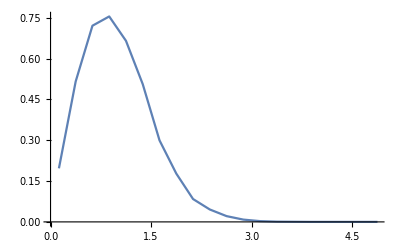

```mathematica
ListPlot[test[[1;;20]],Joined->True]
```

```mathematica
PBrody[1.0,x]
```

1.5708 ⅇ^(-0.785398 x^2.) x^1.

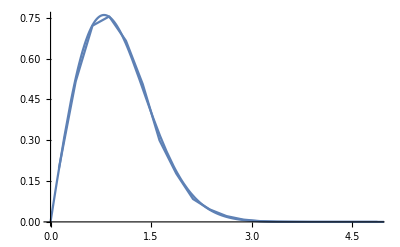

```mathematica
p1=ListPlot[test[[1;;20]],Joined->True];
p2=Plot[PBrody[1.0,x],{x,0,5}];
Show[p1,p2]
```

BrodyS

```mathematica
nlmf=NonlinearModelFit[test[[1;;20]],{PBrody[w,z]},{{w,0.5}},z,Method->"LevenbergMarquardt",ConfidenceLevel->0.9];
```

```mathematica
nlmf["BestFitParameters"]
```

{w→1.02359}

```mathematica
nlmf["ParameterErrors"]
```

{0.0110152}

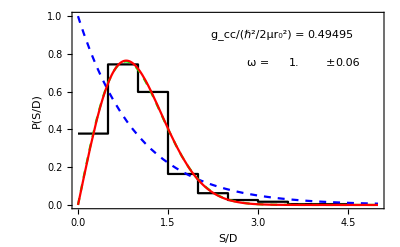

```mathematica
ilamtest=99;
pp=Plot[{PBrody[0,x],PBrody[1,x]},{x,0,5},PlotStyle->{{Blue,Dashed},{Green,Dashed}}];
ph=ListPlot[BCTotals[[ilamtest]],PlotStyle->Black,Joined->True,InterpolationOrder->0,PlotRange->All];
pbrody=Plot[PBrody[w/.nlmT[[ilamtest]]["BestFitParameters"],z],{z,0.0,5},PlotStyle->{Red}];
Show[{ph,pp,pbrody},Frame->True,PlotRange->All,Epilog->{
Text["g_cc/(ℏ^2/2μr_0^2) = ",{3,.9}],
Text[gccVals[[ilamtest]],{4.2,0.9}],
Text["ω = ",{3,.75}],
Text[NumberForm[w/.nlmT[[ilamtest]]["BestFitParameters"],2],{3.6,0.75}],
Text["±",{4.2,0.75}],
Text[NumberForm[nlmT[[ilamtest]]["ParameterErrors"][[1]],1],{4.5,0.75}]
(*Text["Avg Spacing D/(ℏ^2/2μr_0^2) = ",{3.0,0.6}],
Text[avgD[[ienstest,ilamtest]],{4.5,0.6}]*)
},LabelStyle->Large,FrameLabel->{"S/D","P(S/D)"}]
```

### Read in detailed line shape from one of the resonances and try some fits

```mathematica
LineData=Import["~/Code/Nchannel/Square/CODES/FanoLine.dat","Table"];
LineData=LineData[[3;;Length[LineData]]];
iemax=Length[LineData];
BackgroundData=Import["~/Code/Nchannel/Square/CODES/BackgrndLine.dat","Table"];
```

```mathematica
sigma=Table[{LineData[[ie,1]],LineData[[ie,2]]},{ie,iemax}];
ddeldE=Table[{LineData[[ie,1]],LineData[[ie,5]]},{ie,iemax}];
scatamp=Table[{LineData[[ie,1]],LineData[[ie,2]]*LineData[[ie,1]] 1/(2π)1/2},{ie,1,iemax}];
background=Table[{BackgroundData[[ie,1]],BackgroundData[[ie,2]]BackgroundData[[ie,1]] 1/(2π)1/2},{ie,1,iemax}];
delta=Table[{LineData[[ie,1]],π LineData[[ie,4]]-BackgroundData[[ie,3]]},{ie,iemax}];
```

```mathematica
bgdel=Mean[Transpose[BackgroundData][[3]]]
```

-0.663692

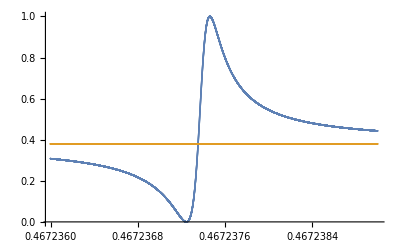

```mathematica
ListPlot[{scatamp,background},PlotRange->All]
```

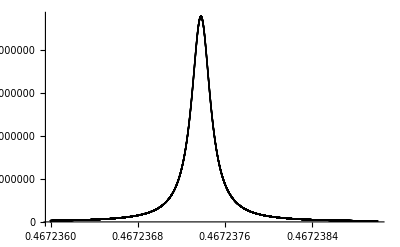

```mathematica
dataplottd=ListPlot[ddeldE,PlotRange->All,PlotStyle->Black]
```

```mathematica
fittedtd=NonlinearModelFit[ddeldE,{(Γ/2)/((EE-Eres)^2+(Γ/2)^2)},{{Eres,0.5},{Γ,.00001}},EE,Method->"LevenbergMarquardt",ConfidenceLevel->0.9];
fittedsigma=NonlinearModelFit[sigma,{(q Γ/2+EE-Eres)^2/((EE-Eres)^2+(Γ/2)^2)/.fittedtd["BestFitParameters"]},{{q,1.0}},EE,Method->"LevenbergMarquardt",ConfidenceLevel->0.9];
fittedscatamp=NonlinearModelFit[scatamp,{(q Γ/2+EE-Eres)^2/((EE-Eres)^2+(Γ/2)^2)/.fittedtd["BestFitParameters"]},{{q,1.0}},EE,Method->"LevenbergMarquardt",ConfidenceLevel->0.9];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

```mathematica
fittedscatamp["BestFitParameters"]
```

{q→0.422439}

```mathematica
fitplottd=Plot[fittedtd[EE],{EE,0.467236,0.467239},PlotRange->All,PlotStyle->Red];
```

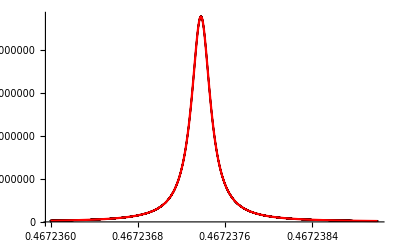

```mathematica
Show[dataplottd,fitplottd]
```

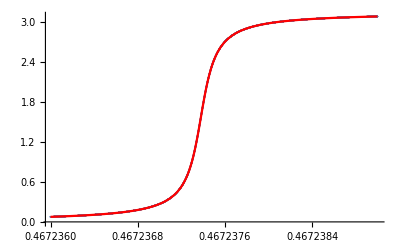

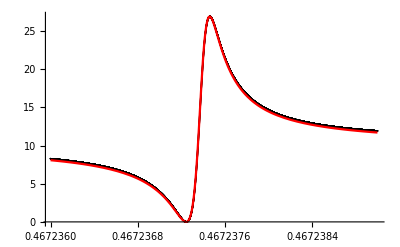

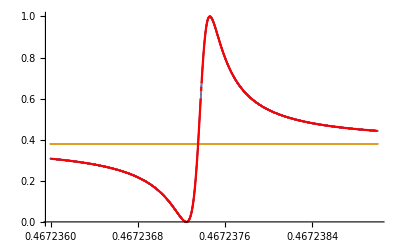

```mathematica
rule=fittedtd["BestFitParameters"];
fitplotsig=Plot[FullSimplify[FanoSigma[σa,q,(EE-Eres)/(Γ/2)]]/.rule/.{σa->10,q->1.3},{EE,0.467236,0.467239},PlotRange->All,PlotStyle->Red];
dataplotsigma=ListPlot[sigma,PlotStyle->Black];
dataplotdelta=ListPlot[delta];
deltacheck[EE_]:=If[EE<Eres/.rule,-ArcTan[(Γ/2)/(EE-Eres)]/.rule,-ArcTan[(Γ/2)/(EE-Eres)]+π/.rule];
fitplotdelta=Plot[If[EE<Eres/.rule,-ArcTan[(Γ/2)/(EE-Eres)]/.rule,-ArcTan[(Γ/2)/(EE-Eres)]+π/.rule],{EE,0.467236,0.467239},PlotRange->All,PlotStyle->Red];
fitplotscatamp=Plot[Sin[deltacheck[EE]+bgdel]^2,{EE,0.467236,0.467239},PlotRange->All,PlotStyle->Red];
dataplotscatamp=ListPlot[{scatamp,background},PlotRange->All];
Show[dataplotdelta,fitplotdelta]
Show[dataplotsigma,fitplotsig,PlotRange->All]
Show[dataplotscatamp,fitplotscatamp]
```

```mathematica
fittedtd["BestFitParameters"]
```

{Eres→0.467237,Γ→2.0942×10^-7}

```mathematica
FanoSigma[σa_,q_,ϵ_]:=σa(q+ϵ)^2/(1+ϵ^2)
```

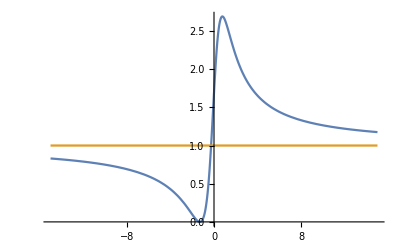

```mathematica
Plot[{FanoSigma[1,1.3,ϵ],1},{ϵ,-15,15},PlotRange->All]
```

```mathematica
rule
```

{Eres→0.467237,Γ→2.0942×10^-7}

```mathematica
FullSimplify[FanoSigma[σa,q,(EE-Eres)/(Γ/2)]]/.rule/.{σa->9,q->1}
```

(9 (-0.934475+2 EE)^2)/(4.38566×10^-14+4 (-0.467237+EE)^2)

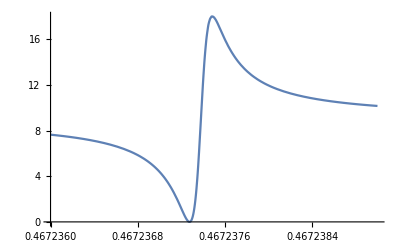

```mathematica
Plot[FullSimplify[FanoSigma[σa,q,(EE-Eres)/(Γ/2)]]/.rule/.{σa->9,q->1},{EE,0.467236,0.467239}]
```

### Try some more lines...

### Read in detailed line shape from one of the resonances and try some fits

```mathematica
LineData=Import["~/Code/Nchannel/Square/CODES/fort.101","Table"];
LineData=LineData[[3;;Length[LineData]]];
iemax=Length[LineData];
BackgroundAmp=Table[{LineData[[ie,1]],LineData[[ie,7]]},{ie,iemax}];
```

```mathematica
sigma=Table[{LineData[[ie,1]],LineData[[ie,2]]},{ie,iemax}];
zclose=Table[{LineData[[ie,1]], Log[LineData[[ie,3]]]},{ie,iemax}];
ddeldE=Table[{LineData[[ie,1]],LineData[[ie,5]]},{ie,iemax}];
scatamp=Table[{LineData[[ie,1]],LineData[[ie,2]]*LineData[[ie,1]] 1/(2π)1/2},{ie,1,iemax}];
phaseopi=Table[{LineData[[ie,1]],LineData[[ie,8]]-LineData[[ie,9]]},{ie,1,iemax}];
```

```mathematica
p1=ListPlot[{scatamp,BackgroundAmp},Joined->True,PlotStyle->{{Black},{Red}},PlotRange->{All,All}];
```

```mathematica
Resonances=Import["~/Code/Nchannel/Square/CODES/fort.801","Table"];NumRes=Length[Resonances];
```

```mathematica
ResLines=Table[ssbg  (EE-ER+q Γ/2)^2/((EE-ER)^2+(Γ/2)^2)/.{ssbg->Resonances[[ires,6]],ER->Resonances[[ires,2]],Γ->Resonances[[ires,4]],q->Resonances[[ires,5]]},{ires,1,NumRes}];
```

```mathematica
resplots=Table[Plot[Evaluate[ResLines[[ires]]],{EE,Resonances[[ires,2]]-3Resonances[[ires,4]],Resonances[[ires,2]]+3Resonances[[ires,4]]},PlotStyle->{Blue,Dashed},PlotRange->All],{ires,1,NumRes}];
```

```mathematica
pmanualresline=Plot[ssbg  (EE-ER+q Γ/2)^2/((EE-ER)^2+(Γ/2)^2)/.{ssbg->0.075,ER->0.3359,Γ->1.4Resonances[[1,4]],q->Resonances[[1,5]]},{EE,0.332,0.34},PlotStyle->Green,PlotRange->All];
pp2=Show[p1,resplots,Frame->True,LabelStyle->Large,FrameLabel->{"Energy","sin^2(δ_0)"},PlotRange->All,PlotRange->{{0.33,.34},{0,1}}]
```

-Graphics-

```mathematica
pphase=ListPlot[phaseopi,PlotRange->All,Joined->True,PlotStyle->{{Green},{Red}}];
```

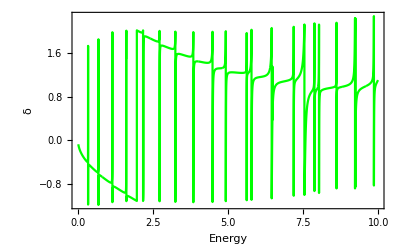

```mathematica
Show[pphase,Frame->True,LabelStyle->Large,FrameLabel->{"Energy","δ"}]
```

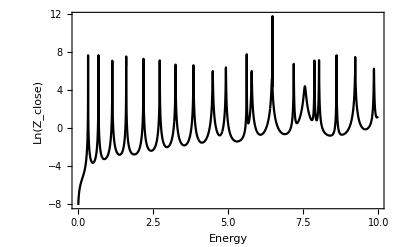

```mathematica
pzc=ListPlot[zclose,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"Energy","Ln(Z_close)"},LabelStyle->Large,PlotStyle->Black]
```

```mathematica
Mean[ LineData[[1;;iemax,3]]]
```

13.5708

```mathematica
pp2=Show[p1,resplots,PlotRange->{{0,10},{0,1}},Frame->True,LabelStyle->Large,FrameLabel->{"Energy","sin^2(δ_0)"}]
```

-Graphics-

```mathematica
pp2=Show[p1,resplots,PlotRange->{{0,10},{0,1}},Frame->True,LabelStyle->Large,FrameLabel->{"Energy","sin^2(δ_0)"}]
```

-Graphics-

```mathematica
pp2=Show[p1,resplots,PlotRange->{All,All},Frame->True,LabelStyle->Large,FrameLabel->{"Energy","sin^2(δ_0)"}]
```

-Graphics-

```mathematica
pp2=Show[p1,resplots,PlotRange->{{6.5,7.5},All},Frame->True,LabelStyle->Large,FrameLabel->{"Energy","sin^2(δ_0)"}]
```

-Graphics-

```mathematica
Show[pp1,pp2]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[pp1,-Graphics-]

```mathematica
pz=ListPlot[{zclose,ddeldE},Joined->True,PlotStyle->{Black,Red},Frame->True,LabelStyle->Large,PlotRange->{{5.02,5.04},{0,9}},PlotRange->{All,All}]
```

-Graphics-

```mathematica
Show[pz,pp2,GridLines->Automatic,PlotRange->{{0.3,0.45},{0,2}}]
```

-Graphics-

```mathematica
xr1={6.66,6.72}
```

{6.66,6.72}

```mathematica
dataplottd=ListPlot[ddeldE,PlotStyle->Black,Joined->True,PlotRange->{All,All}]
```

-Graphics-

```mathematica
FindPeaks[ddeldE]
```

{{1,0.001},{31,0.00474934},{33,0.0049993},{35,0.00524926},{37,0.00549921},{39,0.00574917},{41,0.00599912},{43,0.00624908},{45,0.00649904},{47,0.00674899},{49,0.00699895},{51,0.00724891},{53,0.00749886},37395,{79971,9.9955},{79973,9.99575},{79975,9.996},{79977,9.99625},{79979,9.9965},{79981,9.99675},{79983,9.997},{79985,9.99725},{79987,9.9975},{79989,9.99775},{79991,9.998},{79993,9.99825},{79995,9.9985}}
 |  |  |  |

```mathematica
fittedtd=NonlinearModelFit[ddeldE,{(Γ/2)/((EE-Eres)^2+(Γ/2)^2)},{{Eres,0.5},{Γ,.00001}},EE,Method->"LevenbergMarquardt",ConfidenceLevel->0.9];
fittedsigma=NonlinearModelFit[sigma,{(q Γ/2+EE-Eres)^2/((EE-Eres)^2+(Γ/2)^2)/.fittedtd["BestFitParameters"]},{{q,1.0}},EE,Method->"LevenbergMarquardt",ConfidenceLevel->0.9];
fittedscatamp=NonlinearModelFit[scatamp,{(q Γ/2+EE-Eres)^2/((EE-Eres)^2+(Γ/2)^2)/.fittedtd["BestFitParameters"]},{{q,1.0}},EE,Method->"LevenbergMarquardt",ConfidenceLevel->0.9];
```

```mathematica
fittedscatamp["BestFitParameters"]
```

{q→2884.82}

```mathematica
fitplottd=Plot[fittedtd[EE],{EE,0.467236,0.467239},PlotRange->All,PlotStyle->Red];
```

```mathematica
Show[dataplottd,fitplottd]
```

-Graphics-

```mathematica
rule=fittedtd["BestFitParameters"];
fitplotsig=Plot[FullSimplify[FanoSigma[σa,q,(EE-Eres)/(Γ/2)]]/.rule/.{σa->10,q->1.3},{EE,0.467236,0.467239},PlotRange->All,PlotStyle->Red];
dataplotsigma=ListPlot[sigma,PlotStyle->Black];
dataplotdelta=ListPlot[delta];
deltacheck[EE_]:=If[EE<Eres/.rule,-ArcTan[(Γ/2)/(EE-Eres)]/.rule,-ArcTan[(Γ/2)/(EE-Eres)]+π/.rule];
fitplotdelta=Plot[If[EE<Eres/.rule,-ArcTan[(Γ/2)/(EE-Eres)]/.rule,-ArcTan[(Γ/2)/(EE-Eres)]+π/.rule],{EE,0.467236,0.467239},PlotRange->All,PlotStyle->Red];
fitplotscatamp=Plot[Sin[deltacheck[EE]+bgdel]^2,{EE,0.467236,0.467239},PlotRange->All,PlotStyle->Red];
dataplotscatamp=ListPlot[{scatamp,background},PlotRange->All];
Show[dataplotdelta,fitplotdelta]
Show[dataplotsigma,fitplotsig,PlotRange->All]
Show[dataplotscatamp,fitplotscatamp]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
fittedtd["BestFitParameters"]
```

{Eres→0.467237,Γ→2.0942×10^-7}

```mathematica
FanoSigma[σa_,q_,ϵ_]:=σa(q+ϵ)^2/(1+ϵ^2)
```

```mathematica
Plot[{FanoSigma[1,1.3,ϵ],1},{ϵ,-15,15},PlotRange->All]
```

-Graphics-

```mathematica
rule
```

{Eres→0.467237,Γ→2.0942×10^-7}

```mathematica
FullSimplify[FanoSigma[σa,q,(EE-Eres)/(Γ/2)]]/.rule/.{σa->9,q->1}
```

(9 (-0.934475+2 EE)^2)/(4.38566×10^-14+4 (-0.467237+EE)^2)

```mathematica
Plot[FullSimplify[FanoSigma[σa,q,(EE-Eres)/(Γ/2)]]/.rule/.{σa->9,q->1},{EE,0.467236,0.467239}]
```

-Graphics-

```mathematica
FullSimplify[(Cot[δ-δa]+Cot[δa])^2/(1+Cot[δ-δa]^2)]
```

Csc[δa]^2 Sin[δ]^2

```mathematica
FullSimplify[FanoSigma[σa,q,(EE-ER)/(Γ/2)]]
```

((2 EE-2 ER+q Γ)^2 σa)/(4 (EE-ER)^2+Γ^2)

## data from squarenew.f90

```mathematica
Data=Import["~/Code/Nchannel/Square/CODES/fort.101","Table"];
Data=DeleteCases[Data,{}];
iemax = Length[Data];
sigma=Table[{Data[[ie,2]],Data[[ie,10]]},{ie,iemax}];
logzclose=Table[{Data[[ie,2]], Log[Data[[ie,6]]]},{ie,iemax}];
alsqr=Table[{Data[[ie,2]],Data[[ie,5]]},{ie,1,iemax}];
albgsqr=Table[{Data[[ie,2]],Sin[Data[[ie,8]]]^2},{ie,1,iemax}];
phaseopi=Table[{Data[[ie,2]],Data[[ie,11]]},{ie,1,iemax}];
timedelay=Table[{Data[[ie,2]],Data[[ie,12]]},{ie,1,iemax}];
ascat = Table[{Data[[ie,2]],Data[[ie,4]]},{ie,1,iemax}];
abg=  Table[{Data[[ie,2]],Data[[ie,13]]},{ie,1,iemax}];
BSdet = Table[{Data[[ie,2]],Data[[ie,7]]},{ie,1,iemax}];
```

```mathematica
padding={{100,10},{50,10}};yrange={-100,100};xrange=All;pabg=ListPlot[abg,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","a_bg/r_0"},LabelStyle->{16},PlotRange->{xrange,{-1000,1000}},ImagePadding->padding,GridLines->Automatic];
palsqr=ListPlot[{alsqr,albgsqr},Joined->True,PlotStyle->{{Black},{Red,Dashed}},Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","sin^2(δ)"},LabelStyle->{16},PlotRange->{xrange,All},ImagePadding->padding,GridLines->Automatic];
psigma=ListPlot[sigma,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","σ/r_0^2"},LabelStyle->{16},PlotRange->{xrange,yrange},ImagePadding->padding,GridLines->Automatic];
pstair=ListPlot[phaseopi,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","δ_0/π"},LabelStyle->{16},PlotRange->{xrange,All},ImagePadding->padding,GridLines->Automatic];
plzc=ListPlot[logzclose,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","Ln(z_close)"},LabelStyle->{16},PlotRange->{xrange,All},ImagePadding->padding,GridLines->Automatic];
ptd=ListPlot[timedelay,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","((τ ℏ)/(2  μ SubsuperscriptBox[r, 0, 2]))"},LabelStyle->{16},PlotRange->{xrange,All},ImagePadding->padding,GridLines->Automatic];
pascat=ListPlot[ascat,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","a/r_0"},LabelStyle->{16},PlotRange->{xrange,yrange},ImagePadding->padding,GridLines->Automatic];
pbsdet=ListPlot[BSdet,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","Det[BS]"},LabelStyle->{16},PlotRange->{xrange,{-1,1}},ImagePadding->padding,GridLines->Automatic];
```

```mathematica
GraphicsGrid[{{palsqr},{pascat},{pbsdet},{plzc},{pstair},{pabg},{ptd}}]
```

-Graphics-

```mathematica
Resonances=Import["~/Code/Nchannel/Square/CODES/fort.801","Table"];NumRes=Length[Resonances];
ResLines=Table[ssbg  (EE-ER+q Γ/2)^2/((EE-ER)^2+(Γ/2)^2)/.{ssbg->Resonances[[ires,6]],ER->Resonances[[ires,2]],Γ->Resonances[[ires,4]],q->Resonances[[ires,5]]},{ires,1,NumRes}];
resplots=Table[Plot[Evaluate[ResLines[[ires]]],{EE,Resonances[[ires,2]]-2Resonances[[ires,4]],Resonances[[ires,2]]+2Resonances[[ires,4]]},PlotStyle->{Blue,Dashed},PlotRange->All],{ires,1,NumRes}];
```

```mathematica
Show[{palsqr,resplots},PlotRange->{All,All}]
```

-Graphics-

```mathematica
DataFine=Import["~/Code/Nchannel/Square/CODES/fort.10001","Table"];
DataFine=DeleteCases[DataFine,{}];
iemaxF = Length[DataFine];
sigmaF=Table[{DataFine[[ie,2]],DataFine[[ie,10]]},{ie,iemax}];
logzcloseF=Table[{DataFine[[ie,2]], Log[DataFine[[ie,6]]]},{ie,iemax}];
alsqrF=Table[{DataFine[[ie,2]],DataFine[[ie,5]]},{ie,1,iemax}];
albgsqrF=Table[{DataFine[[ie,2]],Sin[DataFine[[ie,8]]]^2},{ie,1,iemax}];
phaseopiF=Table[{DataFine[[ie,2]],DataFine[[ie,11]]},{ie,1,iemax}];
timedelayF=Table[{DataFine[[ie,2]],DataFine[[ie,12]]},{ie,1,iemax}];
ascatF = Table[{DataFine[[ie,2]],DataFine[[ie,4]]},{ie,1,iemax}];
abgF=  Table[{DataFine[[ie,2]],DataFine[[ie,13]]},{ie,1,iemax}];
BSdetF = Table[{DataFine[[ie,2]],DataFine[[ie,7]]},{ie,1,iemax}];

palsqrF=ListPlot[{alsqrF,albgsqrF},Joined->False,PlotStyle->{{Black},{Red,Dashed}},Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","sin^2(δ)"},LabelStyle->{16},PlotRange->{xrange,All},ImagePadding->padding,GridLines->Automatic]
-Graphics-
ptdF=ListPlot[timedelayF,Joined->False,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","((τ\ℏ)/(2  μ\SubsuperscriptBox[r, 0, 2]))"},LabelStyle->{16},PlotRange->{xrange,All},ImagePadding->padding,GridLines->Automatic];
```

```mathematica
Show[{ptd,ptdF},PlotRange->{{0.60,0.62},All}]
```

-Graphics-

tan δ = (k j'(ka) - γ j(ka))/(k n'(ka) - γ n(ka))

```mathematica
γ=FullSimplify[D[Log[SphericalBesselJ[0,α r]/r],r]/.{α->√(EE+V0),r->1}]
```

-2+√(EE+V0) Cot[√(EE+V0)]

```mathematica
td=FullSimplify[(k D[SphericalBesselJ[0,kr],kr],-γ SphericalBesselJ[0,k r])/(k D[SphericalBesselY[0,kr],kr],-γ SphericalBesselY[0,k r])]/.{kr->√EE,k->√EE,r->1}
```

```mathematica
td
```

(√EE-√(EE+V0) Cot[√(EE+V0)] Tan[√EE])/(√(EE+V0) Cot[√(EE+V0)]+√EE Tan[√EE])

For the square well (single channel):

k cot δ =(α cot αa  + k tan ka)/(1-α/k cot αa tan ka)

cot δ =(α cot αa  + k tan ka)/(k-α cot αa tan ka)

tan δ =(k-α cot αa tan ka)/(α cot αa  + k tan ka)

```mathematica
td=(k-α Cot[α]Tan[k])/(α Cot[α]+k Tan[k])/.{α->√(EE+V0),k->√EE}
```

(√EE-√(EE+V0) Cot[√(EE+V0)] Tan[√EE])/(√(EE+V0) Cot[√(EE+V0)]+√EE Tan[√EE])

```mathematica
Manipulate[Plot[ArcTan[(√EE-√(EE+V0) Cot[√(EE+V0)] Tan[√EE])/(√(EE+V0) Cot[√(EE+V0)]+√EE Tan[√EE])],{EE,0,10},PlotRange->{-π,π}],{V0,0,10}]
```

```mathematica
Plot[ArcTan[td]/.V0->10,{EE,0,10}]
```

-Graphics-

```mathematica
Plot[(-√EE)/td/.EE->0.00001,{V0,0,20}]
```

-Graphics-

```mathematica
GraphicsGrid[{{palsqr},{psigma},{pstair},{plzc},{ptd},{pascat}}]
```

-Graphics-

### A better way to find the time derivative?

(ⅆ sin^2 δ)/ⅆE=2sin δ cos δ ⅆδ/ⅆE

but the time delay is τ=2 ⅆδ/ⅆE, so

(ⅆ sin^2 δ)/ⅆE=2sin δ cos δ τ/2

τ=1/(sin δ cos δ)(ⅆ(sin^2 δ))/ⅆE

```mathematica
Data=Import["~/Code/Nchannel/Square/CODES/fort.101","Table"];
Data=DeleteCases[Data,{}];
iemax = Length[Data];
sigma=Table[{Data[[ie,1]],Data[[ie,5]]},{ie,iemax}];
logzclose=Table[{Data[[ie,1]], Log[Data[[ie,4]]]},{ie,iemax}];
alsqr=Table[{Data[[ie,1]],Data[[ie,3]]},{ie,1,iemax}];
phaseopi=Table[{Data[[ie,1]],Data[[ie,6]]},{ie,1,iemax}];
```

```mathematica
ListPlot[alsqr,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","sin^2(δ)"},LabelStyle->{16},PlotRange->{All,All}]
```

-Graphics-

```mathematica
ListPlot[logzclose,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","Ln(zclose)"},LabelStyle->{16},PlotRange->{All,All}]
```

-Graphics-

```mathematica
ListPlot[sigma,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","σ/r_0^2"},LabelStyle->{16},PlotRange->{All,All}]
```

-Graphics-

```mathematica
ListPlot[alsqr,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","sin^2(δ)"},LabelStyle->{16},PlotRange->{{0.5875,0.590},All}]
```

-Graphics-

```mathematica
D[Tan[x],x]
```

Sec[x]^2